```mathematica
<<Geometry`
```

## TEST1

### Case 1

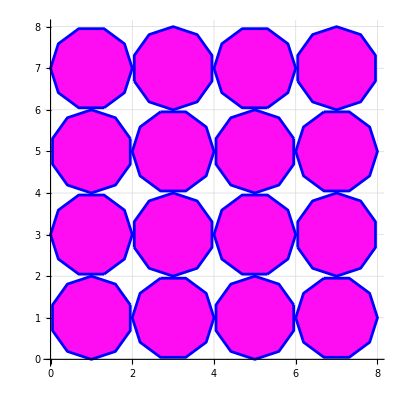

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[10,RGBColor[1,.05,.95,.1]][[1]],{1,1}],{Blue,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr1
```

### Case 2

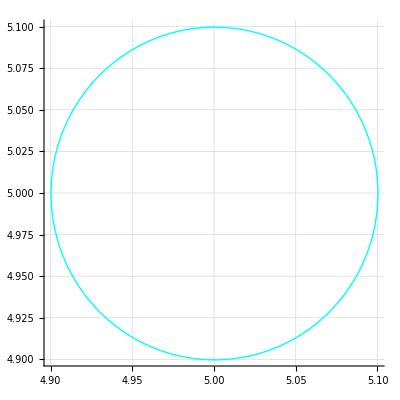

```mathematica
cCircle[{5,5},.1]//toGL//gr1
```

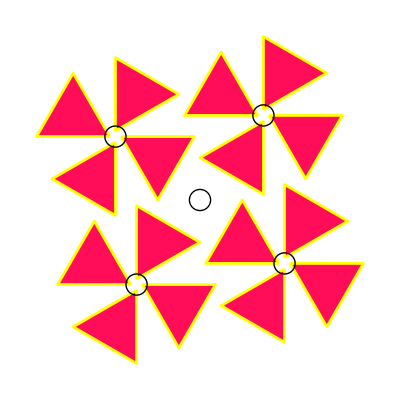

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]
dpoly:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
dpoly:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
Nest[teil,dpoly,2]//toGL//gr
```

## TEST2

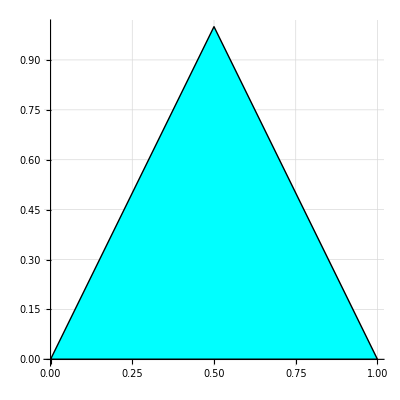

```mathematica
{{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0, 1, 1],1}},{GrayLevel[0],1,0.0025,2 π,2 π}}//toGL//gr1
```

```mathematica
sym4rot[figke_]:= Module[{rotp},
rotp={1,1};
tra3[Scale[{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]},.5],{-.5,-.5}]
]
sym4ref[figke_]:= Module[{rotp},
rotp={1,1};
tra3[Scale[{figke,ref3[figke,{{1,0},rotp}],rot3[figke,{π,rotp}],ref3[figke,{{0,1},rotp}]},.5],{-.5,-.5}]
]
dpoly:={{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.0025,2 π,2 π}}
dpoly:={{{{1,{{0.0,0.4},{0.5,0.0},{0.5,0.5},{1.0,0.75},{0.5,1.0},{0.0,0.6}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.005,2 π,2 π}}}
Nest[sym4ref,dpoly,4]//toGL//gr
```

-Graphics-

```mathematica
dpoly:={{{1,{{0,0},{1,0},{0.5,1}}},{RGBColor[0.63, 0.81, 1.],1}},{RGBColor[0.92, 0.09, 0.1],1,0.0025,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.7,0.2},{1,1},{0,1}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
sym4rot[sym4ref[sym4rot[sym4rot[dpoly]]]]//toGL//gr
```

-Graphics-

## temp-2

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.7,0.2},{1,1},{0,1}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,1},{0.25,1},{0,0.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.05,2 π,2 π}}
```

```mathematica
Table[ind[[k]][dpoly3]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Pythagorean Tiling

### Functions for lines

```mathematica
ClearAll[lFun1]
lFun1[point1:pnt,point2:pnt]:=Module[{a,b},
{a,b}=LinearSolve[{{point1[[1]],1},{point2[[1]],1}},{point1[[2]],point2[[2]]}];
Print[a];
Print[b];
Function[x,a x+b]
]
lFun1[point1:pnt,r_Real]:=Module[{a,b},
{a,b}={r,point1[[2]]-r point1[[1]]};
Print[a];
Print[b];
Function[x,r x+b]
]
lFun1[{1,1},{1.5,5}][10]
```

8.

-7.

73.

### Symmetries

### Method

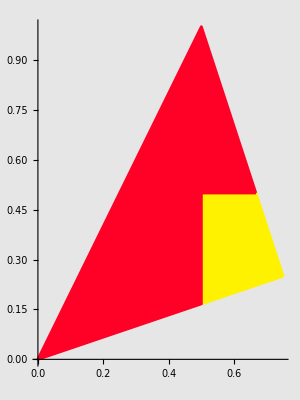

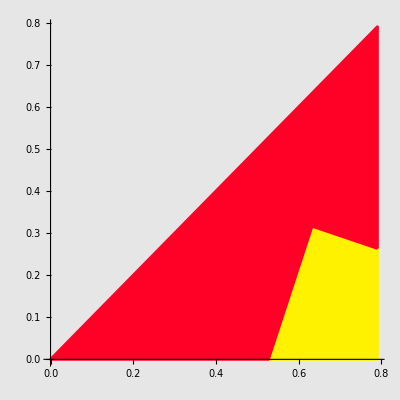

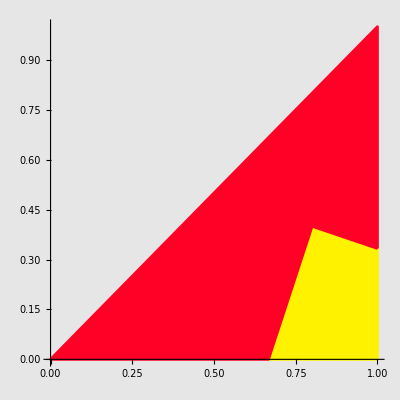

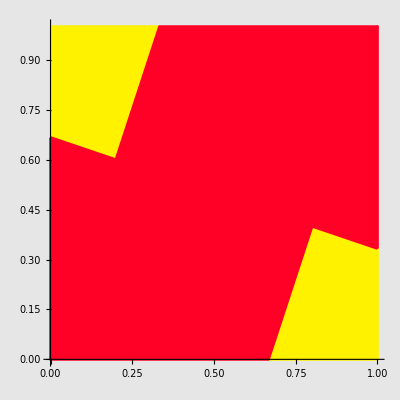

```mathematica
pP={};
pQ={};
pR={};
pS={};
pQ1={};
pR1={};
pS1={};

dpolyA:={{{1,{{0.75,0.25},{2./3,0.5},{0.5,0.5},{0.5,1./6}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[1, 0.9500000000000001, 0],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{2./3,0.5},{0.5,1},{0,0},{0.5,1./6},{0.5,0.5}}},{RGBColor[1, 0, 0.15],1}},{RGBColor[1, 0, 0.15],1,0.005,2 π,2 π}}
dPolyC:={{{1,{{0.25,.5},{2./3,.5}}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}}
dPolyD:={{{1,{{0.5,.5},{.5,1./6}}},{RGBColor[0, 0.9500000000000001, 0],1}},{RGBColor[0.05, 0., 0.65],1,0.0025,2 π,2 π}}

dpoly:={dpolyA,dpolyB,dPolyC,dPolyD}
dpoly//toGL//gr2
dpoly1:=rot3[dpoly,{-ArcTan[1/3],{0,0}}]
dpoly1//toGL//gr2
dpoly2:=sca3[dpoly1,{{1/√((.25)^2+(.75)^2),1/√((.25)^2+(.75)^2)},{0,0}}]
dpoly2//toGL//gr2

(* ERROR *)
dpoly3:={dpoly2,rot3[dpoly2,{π,{0.5,0.5}}]}

dpoly3//toGL//gr2
```

```mathematica
Nest[ind[[4]],dpoly3,1]//toGL//gr
```

-Graphics-

```mathematica
lFun1[{-1.25,0},1./3][0]
lFun1[{0.25,0.50},1./3][0]
```

0.333333

0.416667

0.416667

0.333333

0.416667

0.416667

```mathematica
1/0.4166666666666666666666666667
```

2.4

```mathematica
5./12
```

0.416667

```mathematica
LinearSolve[{{3,1},{-1./3,1}},{2.5,5./12}]
```

{0.625,0.625}

```mathematica
1/.625
```

1.6

```mathematica
5./8
```

0.625

```mathematica
lFun1[{0.75,0.25},1./3][0]
lFun1[{0.25,0.50},-3.][0]
```

0.333333

0.

0.

-3.

1.25

1.25

```mathematica
LinearSolve[{{-1./3,1},{3,1}},{0,5./4}]
```

{0.375,0.125}